```mathematica
python = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
nbdir = StringTake[NotebookDirectory[], {1,-2}];
cwd = ExternalEvaluate[python, "

import sys
import os
nbdir = r'<* nbdir *>'
print(nbdir)
os.chdir(nbdir + '/..')

sys.path.append('.')
from src import ccmodel_v2 as ccmodel
import os 
import pandas as pd
import importlib
import time
import numpy as np
import matplotlib.pyplot as plt

try:
    importlib.reload(ccmodel)   
except:
    print('module have not not imported')
print('Current Directory:', os.getcwd())
"]
```

C:\Users\stnav\OneDrive - HKUST Connect\Academics\Jensen Lab\Python codes\ccmodel_v2\api

Current Directory: C:\Users\stnav\OneDrive - HKUST Connect\Academics\Jensen Lab\Python codes\ccmodel_v2

```mathematica
workingDirectory = FileNameJoin[{ParentDirectory@NotebookDirectory[], "example"}]
```

C:\Users\stnav\OneDrive - HKUST Connect\Academics\Jensen Lab\Python codes\ccmodel_v2\example

```mathematica
ExternalEvaluate[python, "
consts = dict()
consts['number_of_pixels'] = (32, 32)
consts['regions'] = {
    'left' : ((0, 32), (0, 13)),
    'right' : ((0, 32), (21, 32)),
    'all': ((0, 32), (0, 32))
}
consts['number_of_frames'] = 1000
consts['jitter_path'] = os.path.join(os.getcwd(), 'common', '_20200926_JitterCali_DropBadPixel.csv')
consts['working_directory'] = r'<* workingDirectory *>'
consts['write_directory'] = os.path.join(consts['working_directory'], 'analysis')
consts['coincidence_window'] = 2

# modes to initalize counts on object definition
modes = dict()
modes['pixel_accumulated_count'] = False
modes['time_accumulated_count'] = False
modes['pixel_coincidence_count'] = False
modes['time_coincidence_count'] = False

print('Working directory:', consts['working_directory'])
print('Write directory:', consts['write_directory'])
"]
```

Working directory: C:\Users\stnav\OneDrive - HKUST Connect\Academics\Jensen Lab\Python codes\ccmodel_v2\example

Write directory: C:\Users\stnav\OneDrive - HKUST Connect\Academics\Jensen Lab\Python codes\ccmodel_v2\example\analysis

```mathematica
filename = "Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000"
```

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000

```mathematica
ExternalEvaluate[python , "
filters =  ccmodel.filter_generator(consts)

filt = filters.filter_map['nearby']

start = time.time()
a = ccmodel.time_bins(r'<* filename *>', consts, modes, filt, debug=True)
a.adjusted_bins[:, 24, 16] = 0
a.initialize_pixel_accumulated_count()
a.initialize_time_accumulated_count()
a.initialize_coincidence_count(pixel_mode=True, time_mode=True)
a.write_to_file()
a.save_figures()

end = time.time()
print('Elapsed Time:', end-start)
"]
```

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing raw bins

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing jitter bins

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing adjusted bins

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing pixel_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing time_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Initializing pixel and time coincidence_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Writing to file

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Saving Figures

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting pixel_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting time_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting plot_pixel_coincidence_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting plot_time_coincidence_count

Elapsed Time: 1.1189937591552734

```mathematica
pixelAccumulatedCount = ExternalEvaluate[python, "a.pixel_accumulated_count"];
MatrixPlot[pixelAccumulatedCount, PlotLegends->True, ColorFunction->GrayLevel]
```

-Graphics-

```mathematica
pixelCoincidenceCount = ExternalEvaluate[python, "a.pixel_coincidence_count"];
MatrixPlot[pixelCoincidenceCount, PlotLegends->True, ColorFunction->GrayLevel]
```

-Graphics-

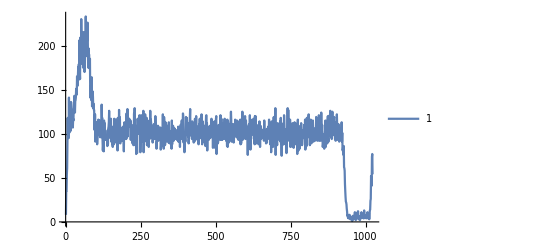

```mathematica
timeAccumulatedCount = ExternalEvaluate[python, "a.time_accumulated_count[1:]"];
ListLinePlot[timeAccumulatedCount, PlotLegends->True, PlotRange->All]
```

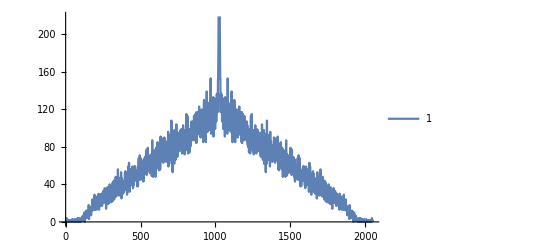

```mathematica
timeCoincidenceCount = ExternalEvaluate[python, "a.time_coincidence_count"];
ListLinePlot[timeCoincidenceCount, PlotLegends->True]
```

```mathematica
ExternalEvaluate[python, "
a.save_figures(show_only=True)
"]
```

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Saving Figures

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting pixel_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting time_accumulated_count

Theta=0_2677165_Frame2_Exp500_Bothinc_frame1000 Plotting plot_pixel_coincidence_count

$Aborted

```mathematica
ExternalEvaluate[python, "
filters.plot_filter_map()
"]
```

Two spots location:

Filter for: self

Filter for: cross

Filter for: nearby

Filter for: all

```mathematica
DeleteObject[ExternalSessions[]]
```